```mathematica
commutator[A_?MatrixQ,B_?MatrixQ]:=A.B-B.A
```

# Lie Group to Lie Algebra

## G2 From Johannes

```mathematica
Subscript[R, m_,n_][ϕ_]:=Table[
If[And[i==j,i!=m,i!=n],
1,
If[i==j,
Cos[ϕ],
If[And[i==m,j==n],
-Sin[ϕ],
If[And[j==m,i==n],
Sin[ϕ],
0
]
]
]
],{i,7},{j,7}];
```

```mathematica
G2families={
Subscript[R, 5,6][-ϕ].Subscript[R, 1,2][-ϕ],
Subscript[R, 5,7][-ϕ].Subscript[R, 1,3][-ϕ],
Subscript[R, 4,5][-ϕ].Subscript[R, 2,3][ϕ],
Subscript[R, 3,5][-ϕ].Subscript[R, 2,4][-ϕ],
Subscript[R, 3,4][-ϕ].Subscript[R, 2,5][ϕ],
Subscript[R, 3,4][-ϕ].Subscript[R, 1,6][-ϕ],
Subscript[R, 2,6][-ϕ].Subscript[R, 1,5][ϕ],
Subscript[R, 3,6][-ϕ].Subscript[R, 1,4][ϕ],
Subscript[R, 5,7][-ϕ].Subscript[R, 4,6][ϕ],
Subscript[R, 3,5][-ϕ].Subscript[R, 1,7][-ϕ],
Subscript[R, 2,7][-ϕ].Subscript[R, 1,4][-ϕ],
Subscript[R, 3,7][-ϕ].Subscript[R, 1,5][ϕ],
Subscript[R, 5,6][-ϕ].Subscript[R, 4,7][-ϕ],
Subscript[R, 6,7][-ϕ].Subscript[R, 4,5][-ϕ]};
```

## SO(n)

```mathematica
SO[n_]:=RotationMatrix[-ϕ,#]&/@Subsets[IdentityMatrix[n],{2}];
```

```mathematica
SOfamilies=SO[5];
```

## Compute Roots of Lie Algebra

### Find cartan generators

Calculate generators:

```mathematica
generators=D[#,ϕ]/.ϕ->0&/@families;
```

select all simple roots:

```mathematica
selectSimpleRootsProcess=NestWhileList[
Function[
{selectedIndices,candidateIndices},
With[{newSimpleRoot=SelectFirst[
candidateIndices,
And@@Map[Function[sel,Norm[commutator[generators[[sel]],generators[[#]]]]==0],selectedIndices]&,
Nothing
]},
{
Append[
selectedIndices,
newSimpleRoot
],
DeleteCases[
candidateIndices,
newSimpleRoot
]
}
]
]@@#&,
{{},Range[Length[generators]]},
Unequal@@(Length@*First/@{##})&,
2,
Length[generators]
];
```

Simple roots indices:

```mathematica
selectSimpleRoots=First@Last[selectSimpleRootsProcess]
```

{1}

Simple roots as cartan, rest as nonCartan

```mathematica
cartan=generators[[selectSimpleRoots]];
nonCartan=generators[[Complement[Range[Length[generators]],selectSimpleRoots]]];
```

### Normalize cartan (skip - no harmful to final visualization)

```mathematica
(*eqs=Join[
Catenate[
Table[
If[i==j,#==1,#==0]&[
Tr[
Dot[
Transpose[Total[c[i,#]cartan[[#]]&/@Range[Length[cartan]]]],
Total[c[j,#]cartan[[#]]&/@Range[Length[cartan]]]
]
]
],
{i,Length[cartan]},
{j,Length[cartan]}
]
]
];
vars=Union[Cases[eqs,_c,Infinity]];*)
```

```mathematica
(*Off[Solve::svars]
sol=Select[Solve[eqs,vars],Length[#]==Length[vars]&];*)
```

```mathematica
(*cartan=Simplify[Table[Total[c[i,#]cartan[[#]]&/@Range[Length[cartan]]],{i,Length[cartan]}]/.sol[[1]]];*)
```

```mathematica
(*normMatrix = Table[Tr[Transpose[cartan[[i]]] . cartan[[j]]], {i, Length[cartan]}, {j, Length[cartan]}];
normMatrix // MatrixForm*)
```

### Solve root vectors

```mathematica
R=r/@Range[Length[nonCartan]];
linComb[j_]=Sum[r[i] nonCartan[[i]],{i,Length[nonCartan]}];
```

```mathematica
vars=Join[R,c/@Range[Length[cartan]]];
```

```mathematica
eqs=Equal[c[#]linComb[#],commutator[cartan[[#]],linComb[#]]]&/@Range[Length[cartan]];
```

```mathematica
Off[Solve::svars]
sol=Solve[eqs,vars];
```

```mathematica
sol//Length
```

2

Convert roots matrices to vectors:

```mathematica
roots=DeleteCases[Select[ⅈ(c/@Range[Length[cartan]]) /.#&/@sol,FreeQ[c]],ConstantArray[0,Length[cartan]]];
roots//Column
```

### Visualize for 2D, 3D cases:

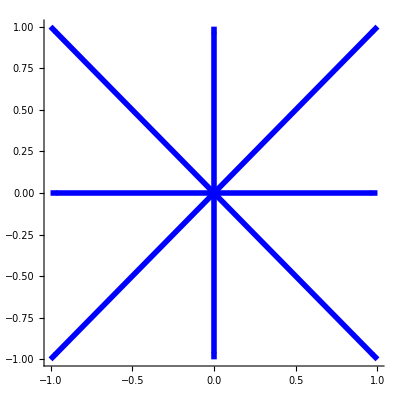

```mathematica
Switch[Length[cartan],2,Graphics,3,Graphics3D][
{Directive[Blue,Thickness->0.01],
Arrow[{ConstantArray[0,Length[cartan]],#}]&/@roots},
Axes->True,AspectRatio->1
]
```

## generatorsToRoots Function Definition - to simplify the procedure

```mathematica
generatorsToRoots[generators_]:=Module[{
cartanIndicesProcess,
cartanIndices,
cartan,nonCartan,
R,r,c,roots,linComb,
eqs,vars,sol
},
cartanIndicesProcess=NestWhileList[
Function[
{selectedIndices,candidateIndices},
With[{newSimpleRoot=SelectFirst[
candidateIndices,
And@@Map[Function[sel,Norm[commutator[generators[[sel]],generators[[#]]]]==0],selectedIndices]&,
Nothing
]},
{
Append[
selectedIndices,
newSimpleRoot
],
DeleteCases[
candidateIndices,
newSimpleRoot
]
}
]
]@@#&,
{{},Range[Length[generators]]},
Unequal@@(Length@*First/@{##})&,
2,
Length[generators]
];

cartanIndices=First@Last[cartanIndicesProcess];

cartan=generators[[cartanIndices]];
nonCartan=generators[[Complement[Range[Length[generators]],cartanIndices]]];

If[
Length[nonCartan]>0,
R=r/@Range[Length[nonCartan]];
linComb[j_]=Sum[r[i] nonCartan[[i]],{i,Length[nonCartan]}];
vars=Join[R,c/@Range[Length[cartan]]];eqs=Equal[c[#]linComb[#],commutator[cartan[[#]],linComb[#]]]&/@Range[Length[cartan]];
Off[Solve::svars];
sol=Solve[eqs,vars];
roots=DeleteCases[Select[ⅈ(c/@Range[Length[cartan]]) /.#&/@sol,FreeQ[c]],ConstantArray[0,Length[cartan]]]
,
roots=IdentityMatrix[Length[cartan]]
];

<|
"cartanGenerators"->cartan,
"nonCartanGenerators"->nonCartan,
"roots"->roots
|>
]
```

# Root Projection

## G2 roots

```mathematica
G2Roots=;
```

## E8 roots

```mathematica
E8Roots=Join[
Union@@(Permutations[Join[#,ConstantArray[0,6]]]&/@Tuples[{-1,1},2]),
Select[Tuples[{1/2,-1/2},8],EvenQ@*Total]];
```

## SO (n)

Get roots from generators

```mathematica
SORoots[n_]:=Block[
{ϕ},
With[{generators=D[#,ϕ]/.ϕ->0&/@SO[n]},
generatorsToRoots[generators]["roots"]
]
]
```

Guess formulas as following (personally guess and verify till n = 14)

```mathematica
SORoots[2]:={{1}};
SORoots[n_/;n>=4&&EvenQ[n]]:=Catenate[Permutations[PadRight[#,n/2]]&/@{{1,1},{-1,1},{-1,-1}}]

SORoots[3]:={{1},{-1}};
SORoots[n_/;n>=5&&OddQ[n]]:=Join[SORoots[n-1],IdentityMatrix[(n-1)/2],-IdentityMatrix[(n-1)/2]]
```

Verification to 10

```mathematica
Function[n,
Sort[Block[
{ϕ},
With[{generators=D[#,ϕ]/.ϕ->0&/@SO[n]},
generatorsToRoots[generators]["roots"]
]
]]==Sort[SORoots[n]]
]/@Range[2,10]
```

{True,True,True,True,True,True,True,True,True}

Verify dimensions of SO(n) groups:

```mathematica
Function[n,Length[SO[n]]==(n(n-1)/2)]/@Range[2,20]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

## SU (n)

```mathematica
SURoots[n_/;n>=2]:=Permutations[PadRight[{1,-1},n]]
```

## Root Analysis Function Definition

```mathematica
rootAnalysis[roots_?MatrixQ]:=Module[{
basis,
rrForm,
coefficients,
positiveRoots,
simpleRoots,
cartan,
reflectionMatrix,
u,v,
roots2D,
gamma,gammaInv,X,Y,
eigenvalues,eigenvecs,
edges,vertexStyles,g,
sortedVertices
},

rrForm=RowReduce[Transpose[roots]];
basis=roots[[Catenate[FirstPosition[1]/@rrForm]]];
coefficients=Transpose[rrForm[[;;Length[basis]]]];
positiveRoots=Pick[roots,Positive@*SelectFirst[#!=0&]/@coefficients,True];
simpleRoots=Complement[positiveRoots,Plus@@@Subsets[positiveRoots,{2}]];

cartan=simpleRoots.Transpose[simpleRoots];

(*reflectionMatrix=Map[
Function[ind,
Block[{M=IdentityMatrix[Length[simpleRoots]]},
M[[ind,ind]]=-1;
Function[k,
Set[
M[[ind,k]],
If[k!=ind&&cartan[[k,ind]]!=0,-cartan[[k,ind]],M[[ind,k]]]
]
]/@Range[Length[simpleRoots]];
M
]
],
Range[Length[simpleRoots]]
];
*)

(*{X,Y}=Dot@@@Transpose[Partition[reflectionMatrix,2]];
gamma=X.Y;
gammaInv=Y.X;*)

{eigenvalues,eigenvecs}=Eigensystem[cartan];
v=Normalize@Dot[eigenvecs[[1]],simpleRoots];
u=Normalize@Dot[eigenvecs[[-1]],simpleRoots];
roots2D=Dot[roots,Transpose[{u,v}]];

(*edges=UndirectedEdge@@@Select[Subsets[roots,{2}],VectorAngle@@#==Pi/3&];*)

edges=UndirectedEdge@@@Select[Subsets[roots,{2}],MemberQ[{0,Pi/6,Pi/3,Pi/4},VectorAngle@@#]&];

vertexStyles=Directive[#,EdgeForm[Black]]&@@@Transpose[
{
Lighter[Hue[#/Length[simpleRoots]]&/@Range[Length[simpleRoots]],.6]
}
];
sortedVertices=SortBy[Norm@*N@*Last][Transpose[{roots,roots2D}]];
g=Graph[
sortedVertices[[All,1]],
edges,
VertexCoordinates->Times[2,sortedVertices[[All,2]]],
VertexStyle->MapThread[Rule,{sortedVertices[[All,1]],Catenate[ConstantArray[#,Length[roots]/Length[simpleRoots]]&/@vertexStyles]}],
EdgeStyle->Directive[Gray,Thin],
ImageSize->900,
Background->Black,
ImageMargins->{{350,350},{0,0}}
];

<|
"simpleRoots"->simpleRoots,
"cartanMatrix"->cartan,
"projectedRoots"->roots2D,
"projectionGraph"->g
|>
]
```

## Main

```mathematica
groupName="SO11";
res=rootAnalysis[SORoots[11]];
g=res["projectionGraph"];
```

## Visualize

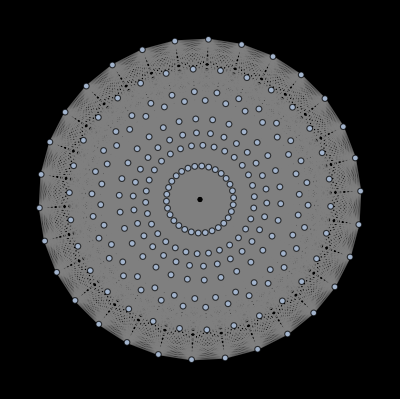
-Graphics-Group E8
vertex number: 240

```mathematica
Labeled[
Show[g,ImageSize->400,ImageMargins->0],
"Group "<>groupName<>"\nvertex number: "<>ToString[VertexCount[g]],
Top
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/"<>groupName<>"-projection.pdf",res["projectionGraph"]]
```

### Aotu-export

```mathematica
Function[n,
Block[{
groupName="SU"<>ToString[n],
res=rootAnalysis[SURoots[n]]
},
Export[NotebookDirectory[]<>"figures/"<>groupName<>"-projection.pdf",res["projectionGraph"]]
]
]/@Range[2,16];
```

```mathematica
Function[n,
Block[{
groupName="SO"<>ToString[n],
res=rootAnalysis[SORoots[n]]
},
Export[NotebookDirectory[]<>"figures/"<>groupName<>"-projection.pdf",res["projectionGraph"]]
]
]/@Range[2,16];
```